```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/trunk/examples/S94_archive/Andrews_2016/surface diffusion

```mathematica
time=300
diffconst=100
binwidth=10
angle=N[ArcTan[450,180]]
lowend=-450
highend=450
branchpt=150
```

300

100

10

0.380506

-450

450

150

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Define functions *)
```

```mathematica
gauss[x_,mu_,sigma_]:=1/(sigma*Sqrt[2*Pi])*Exp[-(x-mu)^2/(2*sigma^2)]
```

```mathematica
Assuming[s>0,Integrate[gauss[x,mu,s],{x,-Infinity,Infinity}]]
```

1

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["branchout.txt","CSV"];
```

```mathematica
simdata
```

{{300,4885,4923,5083,5043,5055,5371,5455,5589,5920,6052,6265,6750,6972,7206,7615,8024,8040,8654,9053,9353,9728,10228,10487,11059,11352,11757,12098,12455,12811,13373,13692,13953,14296,14544,14825,14828,14905,15376,15365,15354,15398,15508,15347,15441,15296,15139,15034,14676,14547,14182,13974,13646,13114,12874,12473,11919,11290,10809,10521,9852,18543,18024,17353,16919,16355,15647,15103,14395,13945,13211,12713,12075,11691,11104,10627,10103,9742,9229,8931,8386,7992,7628,7483,7417,6913,6970,6832,6712,6550,6573},{300,4913,4940,5099,5080,5220,5347,5715,5693,5944,6337,6587,6687,7004,7347,7826,8255,8460,8929,9230,9527,10032,10639,10982,11243,11943,12488,12759,13060,13467,13955,14436,14782,15113,15607,15556,16080,16325,16552,16932,17053,17236,17376,17556,17431,17671,17458,17634,17430,17040,17196,17190,16715,16485,16475,16266,15534,15585,15073,14743,14213,14034,13795,13226,12737,12453,11868,11441,11010,10485,10258,9618,9208,8742,8468,8025,7715,7238,6926,6758,6373,6174,6001,5738,5605,5420,5221,5150,4962,4979,4921}}

```mathematica
simdata1=Drop[simdata[[1]],1]
```

{4885,4923,5083,5043,5055,5371,5455,5589,5920,6052,6265,6750,6972,7206,7615,8024,8040,8654,9053,9353,9728,10228,10487,11059,11352,11757,12098,12455,12811,13373,13692,13953,14296,14544,14825,14828,14905,15376,15365,15354,15398,15508,15347,15441,15296,15139,15034,14676,14547,14182,13974,13646,13114,12874,12473,11919,11290,10809,10521,9852,18543,18024,17353,16919,16355,15647,15103,14395,13945,13211,12713,12075,11691,11104,10627,10103,9742,9229,8931,8386,7992,7628,7483,7417,6913,6970,6832,6712,6550,6573}

```mathematica
simdata2=Drop[simdata[[2]],1]
```

{4913,4940,5099,5080,5220,5347,5715,5693,5944,6337,6587,6687,7004,7347,7826,8255,8460,8929,9230,9527,10032,10639,10982,11243,11943,12488,12759,13060,13467,13955,14436,14782,15113,15607,15556,16080,16325,16552,16932,17053,17236,17376,17556,17431,17671,17458,17634,17430,17040,17196,17190,16715,16485,16475,16266,15534,15585,15073,14743,14213,14034,13795,13226,12737,12453,11868,11441,11010,10485,10258,9618,9208,8742,8468,8025,7715,7238,6926,6758,6373,6174,6001,5738,5605,5420,5221,5150,4962,4979,4921}

```mathematica
Length[simdata2]
```

90

```mathematica
nmolec=Total[simdata2]
Total[simdata1]
```

1000000

1000000

```mathematica
xvector=Table[i,{i,lowend+binwidth/2,highend-binwidth/2,binwidth}]
```

{-445,-435,-425,-415,-405,-395,-385,-375,-365,-355,-345,-335,-325,-315,-305,-295,-285,-275,-265,-255,-245,-235,-225,-215,-205,-195,-185,-175,-165,-155,-145,-135,-125,-115,-105,-95,-85,-75,-65,-55,-45,-35,-25,-15,-5,5,15,25,35,45,55,65,75,85,95,105,115,125,135,145,155,165,175,185,195,205,215,225,235,245,255,265,275,285,295,305,315,325,335,345,355,365,375,385,395,405,415,425,435,445}

```mathematica
Length[xvector]
```

90

```mathematica
simdata1xy=Transpose[{xvector,simdata1}];
```

```mathematica
simdata2xy=Transpose[{xvector,simdata2}];
```

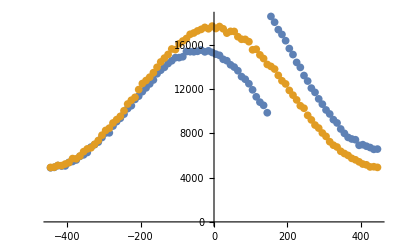

```mathematica
ListPlot[{simdata1xy,simdata2xy}]
```

```mathematica
sigma=N[Cos[angle]*Sqrt[2*time*diffconst]]
```

227.429

```mathematica
theoryfn[x_]=nmolec*binwidth*(gauss[x,0,sigma]+
If[x>branchpt,1/3*gauss[x,0,sigma],-1/3*gauss[2*branchpt-x,0,sigma]]+gauss[x,-(highend-lowend),sigma]+
4/3*gauss[x,highend-lowend,sigma])
```

10000000 (0.00233885 ⅇ^(-9.66667×10^-6 (-900+x)^2)+0.00175414 ⅇ^(-9.66667×10^-6 x^2)+0.00175414 ⅇ^(-9.66667×10^-6 (900+x)^2)+If[x>150,1/3 gauss[x,0,sigma],-1/3 gauss[2 branchpt-x,0,sigma]])

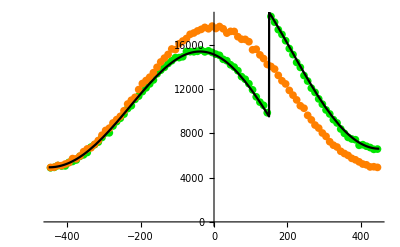

```mathematica
Show[{ListPlot[{simdata1xy,simdata2xy},PlotStyle->{RGBColor[0,0.9,0],Orange}],
Plot[theoryfn[x],{x,lowend,highend},PlotStyle->Black]},Axes->{True,False},AxesStyle->Bold,TicksStyle->Directive[FontOpacity->0,FontSize->1]]
```

```mathematica
errors1=Table[simdata1[[i]]-N[theoryfn[xvector[[i]]]],{i,1,Length[simdata1]}];
```

```mathematica
errors2=Table[simdata2[[i]]-N[theoryfn[xvector[[i]]]],{i,1,Length[simdata2]}];
```

```mathematica
StandardDeviation[errors1]
StandardDeviation[errors2]
```

132.056

2371.78

```mathematica
errors1xy=Transpose[{xvector,errors1}];
```

```mathematica
errors2xy=Transpose[{xvector,errors2}];
```

```mathematica
theoryerror[x_]=Sqrt[theoryfn[x]]
```

1000 √10 √(0.00233885 ⅇ^(-9.66667×10^-6 (-900+x)^2)+0.00175414 ⅇ^(-9.66667×10^-6 x^2)+0.00175414 ⅇ^(-9.66667×10^-6 (900+x)^2)+If[x>150,1/3 gauss[x,0,sigma],-1/3 gauss[2 branchpt-x,0,sigma]])

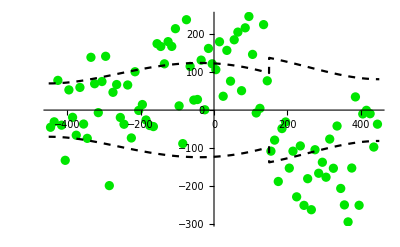

```mathematica
Show[{ListPlot[{errors1xy},PlotStyle->{RGBColor[0,0.9,0]}],Plot[theoryerror[x],{x,lowend,highend},PlotStyle->Directive[Black,Dashed]],Plot[-theoryerror[x],{x,lowend,highend},PlotStyle->Directive[Black,Dashed]]},Axes->{True,False},AxesStyle->Bold,TicksStyle->Directive[FontOpacity->0,FontSize->1]]
```